```mathematica
(*Start*)
r0={1,0};
r1={0,1};
Lx=8;
Ly=8;
J=1;
e=0.0;
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
(*y-periodic*)
Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},If[i<j&&(Abs[l[[i]]-l[[j]]]=={0,Ly-1}),{j,i},"a"]],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
(*xy-periodic*)
Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},If[i<j&&(Abs[l[[i]]-l[[j]]]=={0,Ly-1}||Abs[l[[i]]-l[[j]]]=={Lx-1,0}),{j,i},"a"]],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
(*non-periodic*)
Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
(*old d*)
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0,{0,0,(-1)^(Bonds⟦i,1⟧) d},{0,0,(-1)^(Bonds⟦i,1⟧)d}],{i,1,Length[Bonds]}];
(*new d*)
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,d,(-1)^(Bonds⟦i,1⟧) e},{-d,0,(-1)^(Bonds⟦i,1⟧) e}],{i,1,Length[Bonds]}];
ASublattice=Table[If[EvenQ[Total[l[[i]]]],π,0],{i,1,Lx*Ly}];
MinArgList=Flatten[{Table[{ϕlist⟦i⟧,0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,0},{i,1,Lx*Ly}]},1];
(*Benjamin*)
S[ϕ_,θ_]:={Sin[ϕ]Cos[θ],Cos[ϕ]Cos[θ],-Sin[θ]};
(*Kugelkoordinaten*)
S[ϕ_,θ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]};
```

```mathematica
Hnew=Sum[J*(S[ϕlist[[Bonds[[i,1]]]],θlist⟦Bonds⟦i,1⟧⟧+ASublattice⟦Bonds⟦i,1⟧⟧].S[ϕlist[[Bonds[[i,2]]]],θlist⟦Bonds⟦i,2⟧⟧+ASublattice⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧+ASublattice⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧+ASublattice⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
```

```mathematica
tingeldangelbob=Module[{dd,dangle={},MinArgList=Flatten[{Table[{ϕlist⟦i⟧,(-1)^i RandomReal[]0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,π/2},{i,1,Lx*Ly}]},1]},
For[dd=0.00,dd≤0.3,dd=dd+0.01,
MinArgList=FindMinimum[{Hnew/.d->dd,And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List;
(*MinArgList=NMinimize[{Hnew/.d->10,And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},Flatten[{ϕlist,θlist}]]⟦2⟧/.Rule->List;*)
AppendTo[dangle,Flatten[{dd,Transpose[MinArgList][[2]]}]];
];
dangle
];
```

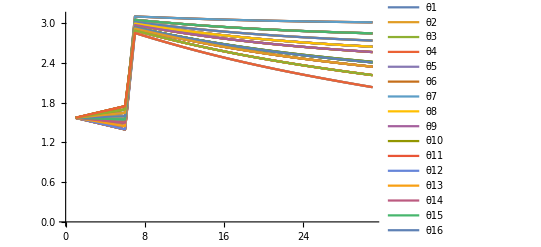
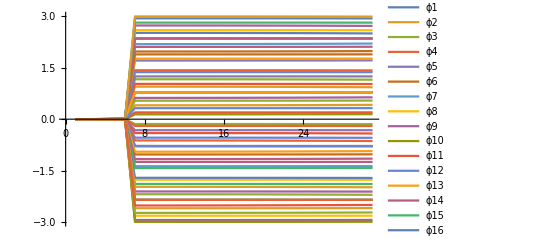

```mathematica
Grid[{{ListLinePlot[Table[tingeldangelbob[[All,i]],{i,Lx*Ly+2,Length[tingeldangelbob[[1]]]}],PlotLegends->θlist]},{
ListLinePlot[Table[tingeldangelbob[[All,i]],{i,2,Lx*Ly+1}],PlotLegends->ϕlist]}}]
```

```mathematica
θarray=ArrayReshape[tingeldangelbob[[-1,Lx*Ly+2;;-1]],{Ly,Lx}];
ϕarray=ArrayReshape[tingeldangelbob[[-1,2;;Lx*Ly+1]],{Ly,Lx}];
Grid[{{ArrayPlot[ϕarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[θarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[Chop[Differences[ϕarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],,ArrayPlot[Chop[Differences[θarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"]}}]
```

-Graphics- | -Graphics- | -Graphics- |  | -Graphics-

```mathematica
TableMinimize[dd_]:=Module[{MinimizeArray,ϕMinimizearray,θMinimizearray},MinimizeArray=NMinimize[{Hnew/.d->dd,And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},Flatten[{ϕlist,θlist}]]⟦2⟧/.Rule->List;
ϕMinimizearray=ArrayReshape[Transpose[MinimizeArray][[2]][[1;;Lx*Ly]],{Ly,Lx}];
θMinimizearray=ArrayReshape[Transpose[MinimizeArray][[2]][[Lx*Ly+1;;-1]],{Ly,Lx}];
{dd,Transpose[MinimizeArray][[2]][[1;;Lx*Ly]],Transpose[MinimizeArray][[2]][[Lx*Ly+1;;-1]]}
]
PlotMinimize[dd_]:=Module[{MinimizeArray,ϕMinimizearray,θMinimizearray},MinimizeArray=NMinimize[{Hnew/.d->dd,And@@Flatten[{Table[ϕlist⟦i⟧>=-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},Flatten[{ϕlist,θlist}]]⟦2⟧/.Rule->List;
ϕMinimizearray=ArrayReshape[Transpose[MinimizeArray][[2]][[1;;Lx*Ly]],{Ly,Lx}];
θMinimizearray=ArrayReshape[Transpose[MinimizeArray][[2]][[Lx*Ly+1;;-1]],{Ly,Lx}];
Grid[{{ArrayPlot[ϕMinimizearray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[θMinimizearray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[Chop[Differences[ϕMinimizearray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],,ArrayPlot[Chop[Differences[θMinimizearray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"]}}]
]
```

```mathematica
ListMinimize=Table[TableMinimize[dd],{dd,0.0,1.0,0.1}];
```

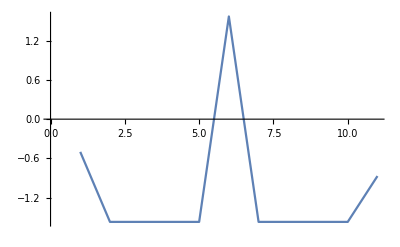

```mathematica
ListLinePlot[ListMinimize[[All,2,3]]]
```

```mathematica
PlotMinimize[1]
```

-Graphics- | -Graphics- | -Graphics- |  | -Graphics-

```mathematica
(*Start new spiral stuff*)
Clear[dy];
r0={1,0};
r1={0,1};
Lx=32;
Ly=32;
J=1;
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
(*non-periodic*)
Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,-dx,0},{dy,0,0}],{i,1,Length[Bonds]}];
ASublattice=Table[If[EvenQ[Total[l[[i]]]],π,0],{i,1,Lx*Ly}];
MinArgList=Flatten[{Table[{ϕlist⟦i⟧,0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,-l⟦i⟧⟦1⟧*ArcTan[dy]},{i,1,Lx*Ly}]},1];
(*Kugelkoordinaten*)
S[ϕ_,θ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]};
```

```mathematica
Hnew=Sum[J*(S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧+ASublattice⟦Bonds⟦i,1⟧⟧].S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧+ASublattice⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧+ASublattice⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧+ASublattice⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
```

```mathematica
dy=0.2;
tingeldangelbob=Module[{ddx,ddy=dy,dangle={},MinArgList=Flatten[{Table[{ϕlist⟦i⟧,0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,l⟦i⟧⟦1⟧*ArcTan[dy]},{i,1,Lx*Ly}]},1]},
For[ddx=0.00,ddx≤ddy,ddx=ddx+0.01,
MinArgList=FindMinimum[{Hnew/.{dx->ddx,dy->ddy},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List;
(*MinArgList=NMinimize[{Hnew/.d->10,And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},Flatten[{ϕlist,θlist}]]⟦2⟧/.Rule->List;*)
AppendTo[dangle,Flatten[{ddx,Transpose[MinArgList][[2]]}]];
];
dangle
];
```

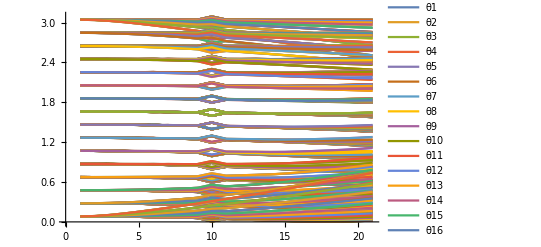
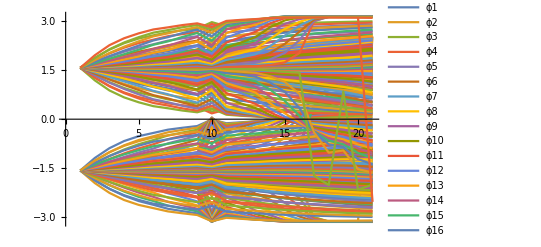

```mathematica
Grid[{{ListLinePlot[Table[tingeldangelbob[[All,i]],{i,Lx*Ly+2,Length[tingeldangelbob[[1]]]}],PlotLegends->θlist]},{
ListLinePlot[Table[tingeldangelbob[[All,i]],{i,2,Lx*Ly+1}],PlotLegends->ϕlist]}}]
```

-Graphics- | -Graphics- | -Graphics- |  | -Graphics-

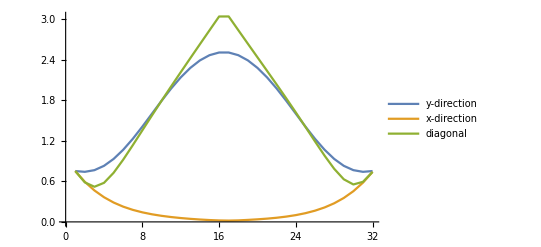

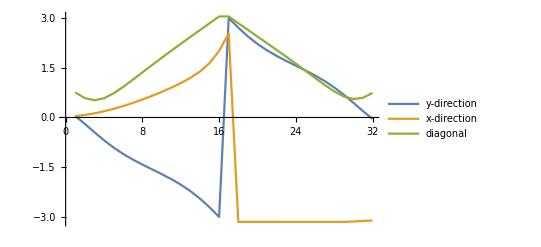

```mathematica
θarray=ArrayReshape[tingeldangelbob[[-1,Lx*Ly+2;;-1]],{Ly,Lx}];
ϕarray=ArrayReshape[tingeldangelbob[[-1,2;;Lx*Ly+1]],{Ly,Lx}];
Grid[{{ArrayPlot[ϕarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[θarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[Chop[Differences[ϕarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],,ArrayPlot[Chop[Differences[θarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"]}}]
ϕplotlist=tingeldangelbob⟦-1,2;;Lx*Ly+1⟧;
θplotlist=tingeldangelbob⟦-1,Lx*Ly+2;;2Lx*Ly+1⟧;
ListLinePlot[{Table[θplotlist⟦Ly*i-Lx+1⟧,{i,1,Lx}],Table[θplotlist⟦i⟧,{i,1,Lx}],Table[θplotlist⟦Ly*i+i+1⟧,{i,0,Lx-1}]},PlotLegends->{"y-direction","x-direction","diagonal"}]
ListLinePlot[{Table[ϕplotlist⟦Ly*i-Lx+1⟧,{i,1,Lx}],Table[ϕplotlist⟦i⟧,{i,1,Lx}],Table[θplotlist⟦Ly*i+i+1⟧,{i,0,Lx-1}]},PlotLegends->{"y-direction","x-direction","diagonal"}]
```

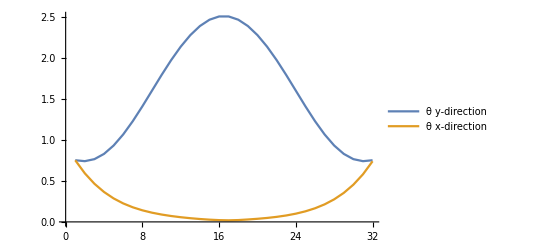

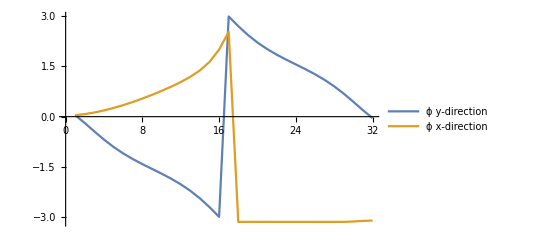

```mathematica
ListLinePlot[{Table[θplotlist⟦Ly*i-Lx+1⟧,{i,1,Lx}],Table[θplotlist⟦i⟧,{i,1,Lx}]},PlotLegends->{"θ y-direction","θ x-direction"}]
ListLinePlot[{Table[ϕplotlist⟦Ly*i-Lx+1⟧,{i,1,Lx}],Table[ϕplotlist⟦i⟧,{i,1,Lx}]},PlotLegends->{"ϕ y-direction","ϕ x-direction"}]
```

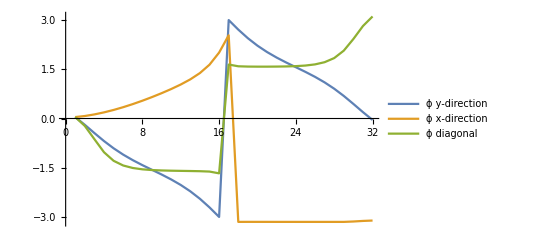

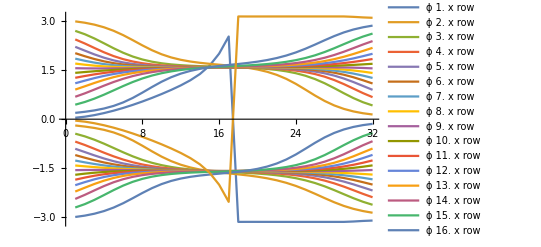

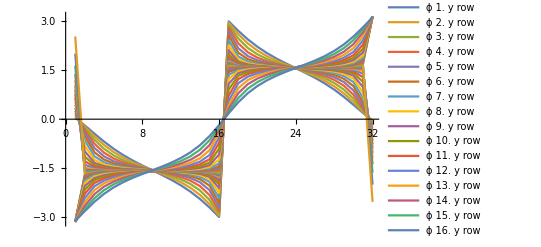

```mathematica
ListLinePlot[{Table[ϕplotlist⟦Ly*i-Lx+1⟧,{i,1,Lx}],Table[ϕplotlist⟦i⟧,{i,1,Lx}],Table[ϕplotlist⟦Ly*i+i+1⟧,{i,0,Lx-1}]},PlotLegends->{"ϕ y-direction","ϕ x-direction","ϕ diagonal"}]
ListLinePlot[Table[Table[ϕplotlist⟦i+n*Lx⟧,{i,1,Lx}],{n,0,Lx-1}],PlotLegends->{Table["ϕ "<>ToString[n+1]<>". x row",{n,0,Lx-1}]}]
ListLinePlot[Table[Table[ϕplotlist⟦Ly*i-Lx+n⟧,{i,1,Lx}],{n,1,Lx-1}],PlotLegends->{Table["ϕ "<>ToString[n+1]<>". y row",{n,0,Lx-1}]}]
```

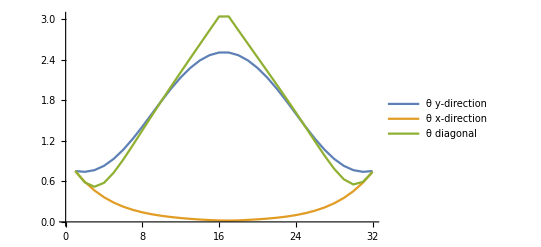

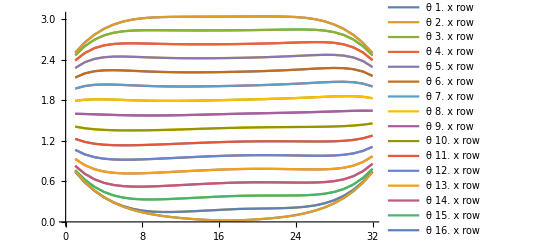

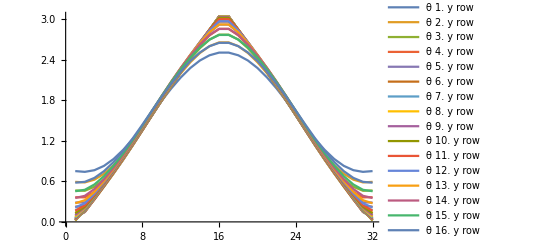

```mathematica
ListLinePlot[{Table[θplotlist⟦Ly*i-Lx+1⟧,{i,1,Lx}],Table[θplotlist⟦i⟧,{i,1,Lx}],Table[θplotlist⟦Ly*i+i+1⟧,{i,0,Lx-1}]},PlotLegends->{"θ y-direction","θ x-direction","θ diagonal"}]
ListLinePlot[Table[Table[θplotlist⟦i+n*Lx⟧,{i,1,Lx}],{n,0,Lx-1}],PlotLegends->{Table["θ "<>ToString[n+1]<>". x row",{n,0,Lx-1}]}]
ListLinePlot[Table[Table[θplotlist⟦Ly*i-Lx+n⟧,{i,1,Lx}],{n,1,Lx-1}],PlotLegends->{Table["θ "<>ToString[n+1]<>". y row",{n,0,Lx-1}]}]
```

```mathematica
dy=0.2;
MinArgList=Flatten[{Table[{ϕlist⟦i⟧,π/2},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,l⟦i⟧⟦2⟧*ArcTan[dy]},{i,1,Lx*Ly}]},1];
(*FindMinimum[{Hnew/.{dx->0.0},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List*)
phianglelist=Transpose[FindMinimum[{Hnew/.{dx->0.0},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List][[2,1;;Lx*Ly]];
thetaanglelist=Transpose[FindMinimum[{Hnew/.{dx->0.0},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List][[2,Lx*Lx+1;;2*Lx*Ly]];
ϕlist=tingeldangelbob⟦-1,2;;Lx*Ly+1⟧;
θlist=tingeldangelbob⟦-1,Lx*Ly+2;;2Lx*Ly+1⟧;
```

```mathematica
(*Start more fancy method???*)
Clear[dy];
r0={1,0};
r1={0,1};
Lx=10;
Ly=10;
J=1;
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
(*non-periodic*)
Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,-dx,0},{dy,0,0}],{i,1,Length[Bonds]}];
ASublattice=Table[If[EvenQ[Total[l[[i]]]],π,0],{i,1,Lx*Ly}];
MinArgList=Flatten[{Table[{ϕlist⟦i⟧,0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,0},{i,1,Lx*Ly}]},1];
(*Kugelkoordinaten*)
S[ϕ_,θ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]};
```

```mathematica
Hnew=Sum[J*(S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧+ASublattice⟦Bonds⟦i,1⟧⟧].S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧+ASublattice⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧+ASublattice⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧+ASublattice⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
```

```mathematica
tingeldangelbob=Module[{dd,step=0.001,dangle={},MinArgList=Flatten[{Table[{ϕlist⟦i⟧,0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,0},{i,1,Lx*Ly}]},1]},
For[dd=0.00,dd≤0.2,dd=dd+step,
MinArgList=FindMinimum[{Hnew/.{dx->dd,dy->dd+step},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List;
MinArgList=FindMinimum[{Hnew/.{dx->dd+step,dy->dd+step},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List;
(*MinArgList=NMinimize[{Hnew/.d->10,And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},Flatten[{ϕlist,θlist}]]⟦2⟧/.Rule->List;*)
AppendTo[dangle,Flatten[{dd,Transpose[MinArgList][[2]]}]];
];
dangle
];
```

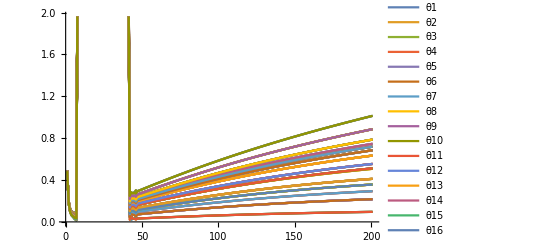
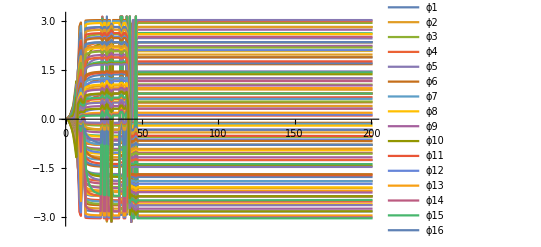

```mathematica
Grid[{{ListLinePlot[Table[tingeldangelbob[[All,i]],{i,Lx*Ly+2,Length[tingeldangelbob[[1]]]}],PlotLegends->θlist]},{
ListLinePlot[Table[tingeldangelbob[[All,i]],{i,2,Lx*Ly+1}],PlotLegends->ϕlist]}}]
```

```mathematica
θarray=ArrayReshape[tingeldangelbob[[-1,Lx*Ly+2;;-1]],{Ly,Lx}];
ϕarray=ArrayReshape[tingeldangelbob[[-1,2;;Lx*Ly+1]],{Ly,Lx}];
Grid[{{ArrayPlot[ϕarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[θarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[Chop[Differences[ϕarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],,ArrayPlot[Chop[Differences[θarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"]}}]
ϕplotlist=tingeldangelbob⟦-1,2;;Lx*Ly+1⟧;
θplotlist=tingeldangelbob⟦-1,Lx*Ly+2;;2Lx*Ly+1⟧;
```

-Graphics- | -Graphics- | -Graphics- |  | -Graphics-

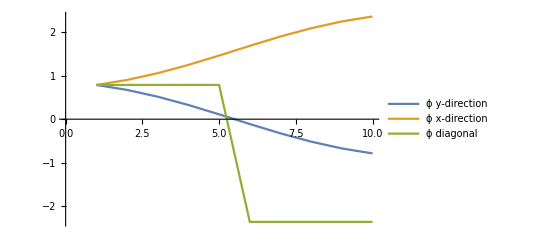

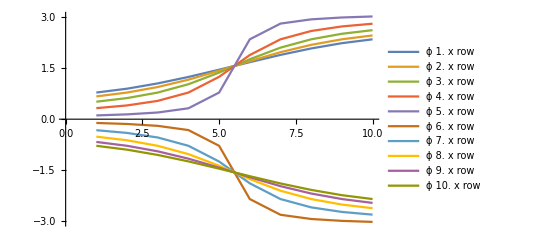

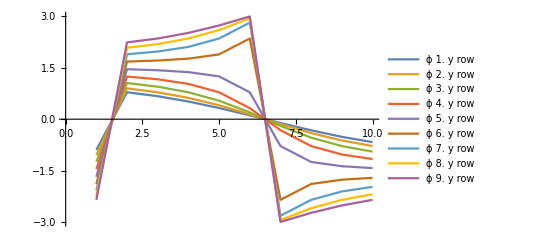

```mathematica
ListLinePlot[{Table[ϕplotlist⟦Ly*i-Lx+1⟧,{i,1,Lx}],Table[ϕplotlist⟦i⟧,{i,1,Lx}],Table[ϕplotlist⟦Ly*i+i+1⟧,{i,0,Lx-1}]},PlotLegends->{"ϕ y-direction","ϕ x-direction","ϕ diagonal"}]
ListLinePlot[Table[Table[ϕplotlist⟦i+n*Lx⟧,{i,1,Lx}],{n,0,Lx-1}],PlotLegends->{Table["ϕ "<>ToString[n+1]<>". x row",{n,0,Lx-1}]}]
ListLinePlot[Table[Table[ϕplotlist⟦Ly*i-Lx+n⟧,{i,0,Lx-1}],{n,1,Lx-1}],PlotLegends->{Table["ϕ "<>ToString[n+1]<>". y row",{n,0,Lx-1}]}]
```

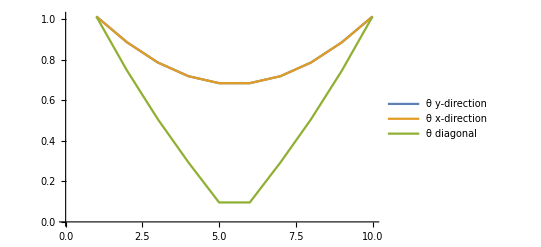

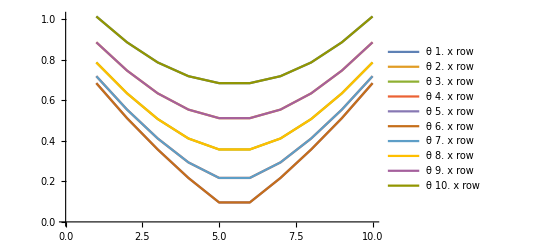

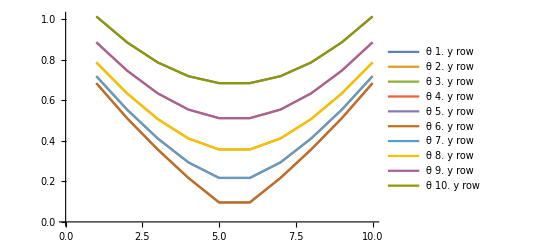

```mathematica
ListLinePlot[{Table[θplotlist⟦Ly*i-Lx+1⟧,{i,1,Lx}],Table[θplotlist⟦i⟧,{i,1,Lx}],Table[θplotlist⟦Ly*i+i+1⟧,{i,0,Lx-1}]},PlotLegends->{"θ y-direction","θ x-direction","θ diagonal"}]
ListLinePlot[Table[Table[θplotlist⟦i+n*Lx⟧,{i,1,Lx}],{n,0,Lx-1}],PlotLegends->{Table["θ "<>ToString[n+1]<>". x row",{n,0,Lx-1}]}]
ListLinePlot[Table[Table[θplotlist⟦Ly*i-Lx+n⟧,{i,1,Lx}],{n,1,Lx}],PlotLegends->{Table["θ "<>ToString[n+1]<>". y row",{n,0,Lx-1}]}]
```

```mathematica
(*scalar triple product on lattice*)
ϕplotlist=tingeldangelbob⟦-1,2;;Lx*Ly+1⟧;
θplotlist=tingeldangelbob⟦-1,Lx*Ly+2;;2Lx*Ly+1⟧;
(*ϕplotlist=Neelstatearglist[[1;;Lx*Ly,2]];
θplotlist=Neelstatearglist[[Lx*Ly+1;;2*Lx*Ly,2]];*)
help=Table[Flatten[Table[{{0.2,0,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y+1)*Lx+1+x⟧,θplotlist⟦(y+1)*Lx+1+x⟧]]},{y,0,Ly-2}]],{x,0,Lx-1}];
testlisty=Table[Flatten[Table[{help[[i]][[j]],0},{i,1,Ly-1}]],{j,1,Lx-1}];
testlistx=Table[Flatten[Table[{0,{0,-0.2,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y)*Lx+x+2⟧,θplotlist⟦(y)*Lx+x+2⟧]]},{x,0,Lx-2}]],{y,0,Ly-1}];
testlist3=Table[{testlistx[[i]],testlisty[[i]]},{i,1,Length[testlistx]-1}];
MatrixPlot[testlistx,PlotLegends->Automatic]
MatrixPlot[testlisty,PlotLegends->Automatic]
MatrixPlot[Flatten[testlist3,1],PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear[bklist]
bklist[κ_]:=Flatten[{dx->tingeldangelbob[[κ,1]],Table[Flatten[{ϕlist,θlist}]⟦i⟧->tingeldangelbob[[κ,2;;]]⟦i⟧,{i,1,2Lx*Ly}]}]
```

```mathematica
tingeldangelbob[[-1,2;;]]
```

{0.785395,0.899424,1.05526,1.2454,1.45942,1.68216,1.89618,2.08632,2.24216,2.35619,0.671366,0.785395,0.948542,1.16532,1.42908,1.7125,1.97625,2.19304,2.35619,2.47022,0.515531,0.622246,0.785393,1.03083,1.37392,1.76764,2.11074,2.35619,2.51934,2.62605,0.325393,0.405464,0.539952,0.785389,1.24946,1.89209,2.35618,2.60163,2.73612,2.81619,0.111372,0.141712,0.196859,0.321315,0.785366,2.35615,2.82026,2.94473,2.99988,3.03022,-0.111372,-0.141712,-0.196859,-0.321315,-0.785366,-2.35615,-2.82026,-2.94473,-2.99988,-3.03022,-0.325393,-0.405464,-0.539952,-0.785389,-1.24946,-1.89209,-2.35618,-2.60163,-2.73612,-2.81619,-0.515531,-0.622246,-0.785393,-1.03083,-1.37392,-1.76764,-2.11074,-2.35619,-2.51934,-2.62605,-0.671366,-0.785395,-0.948542,-1.16532,-1.42908,-1.7125,-1.97625,-2.19304,-2.35619,-2.47022,-0.785395,-0.899424,-1.05526,-1.2454,-1.45942,-1.68216,-1.89618,-2.08632,-2.24216,-2.35619,1.01307,0.885639,0.786338,0.718529,0.684134,0.684133,0.718527,0.786335,0.885635,1.01306,0.88564,0.746162,0.633938,0.553818,0.511526,0.511525,0.553815,0.633933,0.746156,0.885633,0.786339,0.633938,0.50729,0.411333,0.357141,0.35714,0.411329,0.507285,0.633931,0.786332,0.718531,0.553819,0.411334,0.293427,0.21679,0.216787,0.293421,0.411326,0.553811,0.718523,0.684136,0.511529,0.357144,0.216792,0.0959357,0.0959292,0.216783,0.357135,0.51152,0.684127,0.684136,0.511529,0.357144,0.216792,0.0959357,0.0959292,0.216783,0.357135,0.51152,0.684127,0.718531,0.553819,0.411334,0.293427,0.21679,0.216787,0.293421,0.411326,0.553811,0.718523,0.786339,0.633938,0.50729,0.411333,0.357141,0.35714,0.411329,0.507285,0.633931,0.786332,0.88564,0.746162,0.633938,0.553818,0.511526,0.511525,0.553815,0.633933,0.746156,0.885633,1.01307,0.885639,0.786338,0.718529,0.684134,0.684133,0.718527,0.786335,0.885635,1.01306}

```mathematica
dy=0.2;
xspiralstate=Flatten[{{dx->0.2},Table[{ϕlist⟦i⟧->0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧->l⟦i⟧⟦1⟧*ArcTan[dy]+0*l⟦i⟧⟦2⟧*ArcTan[dy]},{i,1,Lx*Ly}]}];
```

```mathematica
l⟦1⟧
```

{0,0}

```mathematica
xspiralstate
```

{dx→0.2,ϕ1→0,ϕ2→0,ϕ3→0,ϕ4→0,ϕ5→0,ϕ6→0,ϕ7→0,ϕ8→0,ϕ9→0,ϕ10→0,ϕ11→0,ϕ12→0,ϕ13→0,ϕ14→0,ϕ15→0,ϕ16→0,ϕ17→0,ϕ18→0,ϕ19→0,ϕ20→0,ϕ21→0,ϕ22→0,ϕ23→0,ϕ24→0,ϕ25→0,ϕ26→0,ϕ27→0,ϕ28→0,ϕ29→0,ϕ30→0,ϕ31→0,ϕ32→0,ϕ33→0,ϕ34→0,ϕ35→0,ϕ36→0,ϕ37→0,ϕ38→0,ϕ39→0,ϕ40→0,ϕ41→0,ϕ42→0,ϕ43→0,ϕ44→0,ϕ45→0,ϕ46→0,ϕ47→0,ϕ48→0,ϕ49→0,ϕ50→0,ϕ51→0,ϕ52→0,ϕ53→0,ϕ54→0,ϕ55→0,ϕ56→0,ϕ57→0,ϕ58→0,ϕ59→0,ϕ60→0,ϕ61→0,ϕ62→0,ϕ63→0,ϕ64→0,ϕ65→0,ϕ66→0,ϕ67→0,ϕ68→0,ϕ69→0,ϕ70→0,ϕ71→0,ϕ72→0,ϕ73→0,ϕ74→0,ϕ75→0,ϕ76→0,ϕ77→0,ϕ78→0,ϕ79→0,ϕ80→0,ϕ81→0,ϕ82→0,ϕ83→0,ϕ84→0,ϕ85→0,ϕ86→0,ϕ87→0,ϕ88→0,ϕ89→0,ϕ90→0,ϕ91→0,ϕ92→0,ϕ93→0,ϕ94→0,ϕ95→0,ϕ96→0,ϕ97→0,ϕ98→0,ϕ99→0,ϕ100→0,θ1→0.,θ2→0.197396,θ3→0.394791,θ4→0.592187,θ5→0.789582,θ6→0.986978,θ7→1.18437,θ8→1.38177,θ9→1.57916,θ10→1.77656,θ11→0.,θ12→0.197396,θ13→0.394791,θ14→0.592187,θ15→0.789582,θ16→0.986978,θ17→1.18437,θ18→1.38177,θ19→1.57916,θ20→1.77656,θ21→0.,θ22→0.197396,θ23→0.394791,θ24→0.592187,θ25→0.789582,θ26→0.986978,θ27→1.18437,θ28→1.38177,θ29→1.57916,θ30→1.77656,θ31→0.,θ32→0.197396,θ33→0.394791,θ34→0.592187,θ35→0.789582,θ36→0.986978,θ37→1.18437,θ38→1.38177,θ39→1.57916,θ40→1.77656,θ41→0.,θ42→0.197396,θ43→0.394791,θ44→0.592187,θ45→0.789582,θ46→0.986978,θ47→1.18437,θ48→1.38177,θ49→1.57916,θ50→1.77656,θ51→0.,θ52→0.197396,θ53→0.394791,θ54→0.592187,θ55→0.789582,θ56→0.986978,θ57→1.18437,θ58→1.38177,θ59→1.57916,θ60→1.77656,θ61→0.,θ62→0.197396,θ63→0.394791,θ64→0.592187,θ65→0.789582,θ66→0.986978,θ67→1.18437,θ68→1.38177,θ69→1.57916,θ70→1.77656,θ71→0.,θ72→0.197396,θ73→0.394791,θ74→0.592187,θ75→0.789582,θ76→0.986978,θ77→1.18437,θ78→1.38177,θ79→1.57916,θ80→1.77656,θ81→0.,θ82→0.197396,θ83→0.394791,θ84→0.592187,θ85→0.789582,θ86→0.986978,θ87→1.18437,θ88→1.38177,θ89→1.57916,θ90→1.77656,θ91→0.,θ92→0.197396,θ93→0.394791,θ94→0.592187,θ95→0.789582,θ96→0.986978,θ97→1.18437,θ98→1.38177,θ99→1.57916,θ100→1.77656}

```mathematica
Hnew/.xspiralstate
```

-174.722

```mathematica
Hnew/.bklist[-1]
```

-182.89

```mathematica
Hnew/.bklist[1]
```

-180.014

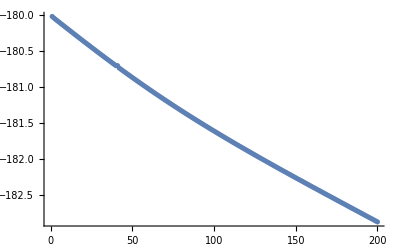

```mathematica
ListPlot[Table[Hnew/.bklist[s],{s,1,Length[tingeldangelbob]}]]
```

```mathematica
Hnew/.bklist[Length[tingeldangelbob]]
```

-182.89

```mathematica
Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[ϕplotlist⟦i+j*Lx+1⟧,(π/2+(-1)^(i+j)*π/2)+θplotlist⟦i+j*Lx+1⟧]}]],{i,0,Lx-1},{j,0,Ly-1}]}]
```

-Graphics3D-

```mathematica
Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[ϕplotlist⟦i+j*Lx+1⟧,(π/2)+θplotlist⟦i+j*Lx+1⟧]}]],{i,0,Lx-1},{j,0,Ly-1}]}]
```

-Graphics3D-

```mathematica
dy=0.2;
xspiralstate=Flatten[{Table[{ϕlist⟦i⟧,0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,l⟦i⟧⟦1⟧*ArcTan[dy]},{i,1,Lx*Ly}]},1];
```

```mathematica
Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[ϕplotlist⟦i+j*Lx+1⟧,π/2*(1-(-1)^ (i+j))+(i+1)*ArcTan[dy]]}]],{i,0,Lx-1},{j,0,Ly-1}]}]
```

-Graphics3D-